```mathematica
Quit[]
```

# Initial Conditions

```mathematica
(*User supplied data*)
m1=1.5;m2=1; λ0=0;λmax=2;
Rinit={1,.5,1.5};
Pinit={1,-4,1};
S1init={1,1,1.3};
S2init={-7.5,-1.5,4.2}
(*end of user supplied  data*)






Linit=Cross[Rinit, Pinit];
Jinit=Linit+S1init+S2init;(* J aligned along z and stays conserved *)
```

{-7.5,-1.5,4.2}

# system of equations

```mathematica
R={Rx[λ],Ry[λ],Rz[λ]};P={Px[λ],Py[λ],Pz[λ]};
S1={S1x[λ],S1y[λ],S1z[λ]};S2={S2x[λ],S2y[λ],S2z[λ]};




eqa=D[R,λ]-( Cross[2 Jinit,R]);
eqb=D[P,λ]-( Cross[2 Jinit,P]);
eqc=D[S1,λ]-( Cross[2 Jinit,S1]);
eqd=D[S2,λ]-( Cross[2 Jinit,S2]);

system0={eqa[[1]]==0,eqa[[2]]==0,eqa[[3]]==0, eqb[[1]]==0,eqb[[2]]==0,eqb[[3]]==0,eqc[[1]]==0,eqc[[2]]==0,eqc[[3]]==0,eqd[[1]]==0,eqd[[2]]==0,eqd[[3]]==0}//Simplify;
initCond = {Rx[λ0] == Rinit[[1]], Ry[λ0] == Rinit[[2]], Rz[λ0] == Rinit[[3]], Px[λ0] == Pinit[[1]], Py[λ0] == Pinit[[2]], Pz[λ0] == Pinit[[3]] , S1x[λ0] ==S1init[[1]], S1y[λ0] ==S1init[[2]], S1z[λ0] == S1init[[3]], S2x[λ0] == S2init[[1]], S2y[λ0] ==S2init[[2]], S2z[λ0] == S2init[[3]]}  ;
sol=DSolve[   system0~Join~initCond  ,  {Rx, Ry, Rz, Px, Py,Pz,S1x, S1y, S1z,S2x, S2y, S2z},λ][[1]];
```

```mathematica
Rx[λ]/.sol/.{λ->λmax}
```

-0.275242

```mathematica
finalvec=Re[{m1,m2,{Rx[λ],Ry[λ],Rz[λ]}/.sol/.{λ->λmax},{Px[λ],Py[λ],Pz[λ]}/.sol/.{λ->λmax},{S1x[λ],S1y[λ],S1z[λ]}/.sol/.{λ->λmax},{S2x[λ],S2y[λ],S2z[λ]}/. sol/.{λ->λmax},λ0,λmax}]
```

{1.5,1,{-0.275242,-1.08362,1.5},{-3.68085,1.85777,1},{0.103159,-1.41045,1.3},{3.76712,6.65648,4.2},0,2}

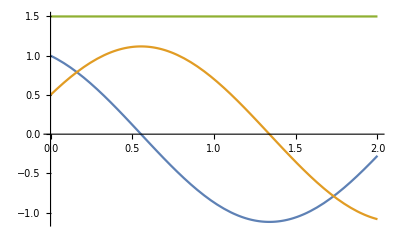

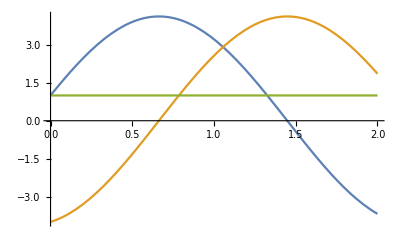

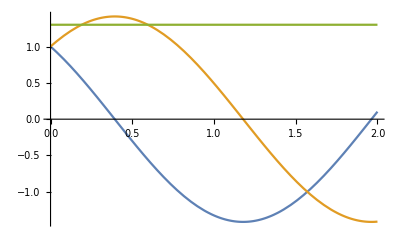

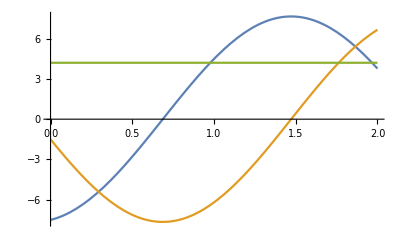

```mathematica
Print[Plot[{Rx[λ]/.sol,Ry[λ]/.sol,Rz[λ]/.sol},{λ,0,λmax}]];
                Print[Plot[{Px[λ]/.sol,Py[λ]/.sol,Pz[λ]/.sol},{λ,0,λmax}]];
                Print[Plot[{S1x[λ]/.sol,S1y[λ]/.sol,S1z[λ]/.sol},{λ,0,λmax}]];
                Print[Plot[{S2x[λ]/.sol,S2y[λ]/.sol,S2z[λ]/.sol},{λ,0,λmax}]];
```

```mathematica
Show[Graphics3D[{{Red,Arrowheads[0.03],Arrow[{{0,0,0},Jinit}]},{Blue,Arrowheads[0.03],Arrow[{{0,0,0},Rinit}]},{Green,Arrowheads[0.03],Arrow[{{0,0,0},Pinit}]},{Brown,Arrowheads[0.03],Arrow[{{0,0,0},S1init}]},{Magenta,Arrowheads[0.03],Arrow[{{0,0,0},S2init}]}}],ParametricPlot3D[Evaluate[{Rx[λ],Ry[λ],Rz[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Blue],ParametricPlot3D[Evaluate[{Px[λ],Py[λ],Pz[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Green],ParametricPlot3D[Evaluate[{S1x[λ],S1y[λ],S1z[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Brown],ParametricPlot3D[Evaluate[{S2x[λ],S2y[λ],S2z[λ]}/. sol],{λ,λ0,λmax},PlotStyle->Magenta],Boxed->False]
```

-Graphics3D-